```mathematica
Exit
```

## Metric

```mathematica
f[r_,q_]=1-2/r (1-Tanh[q^2/(2r)]);
θ=π/2;
gtt=-f[r,q];
grr = -1/gtt;
gθθ = r^2;
gϕϕ = r^2 Sin[θ]^2;
```

## Horizons

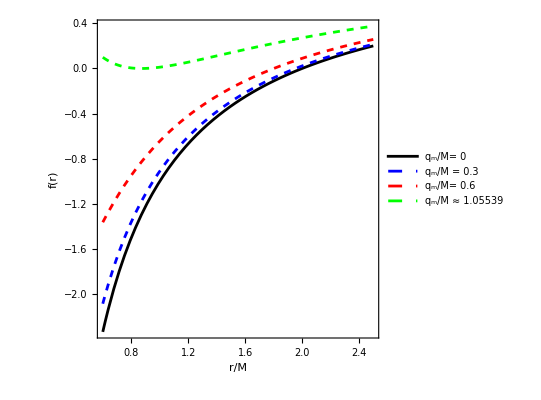

```mathematica
Plot[{f[r,10^-6],f[r,0.3],f[r,0.6],f[r,1.05539]},{r,0.6,2.5},Frame->True,FrameLabel->{"r/M","f(r)"},AspectRatio->1,PlotStyle->{Black,{Blue,Dashed},{Red,Dashed},{Green,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},PlotLegends->Placed[{"q_m/M= 0","q_m/M = 0.3","q_m/M= 0.6","q_m/M ≈ 1.05539"},{Scaled[{0.72,0.26}], {0.4, 0.5}}]]
```

```mathematica
rh[q_] := r/.FindRoot[f[r,q]==0,{r,2}]
```

```mathematica
rh[0.5]
```

1.86624

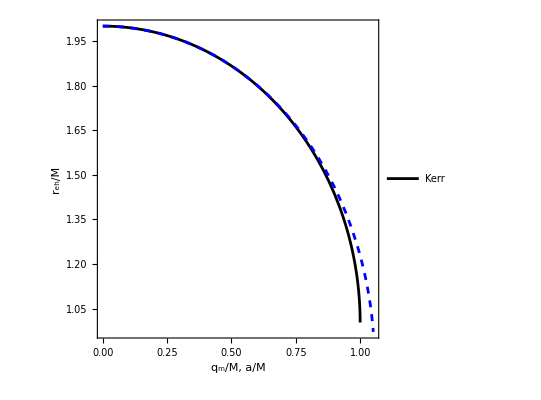

```mathematica
Plot[{1+√(1-q^2),rh[q]},{q,0,1.051},AspectRatio->1,PlotStyle->{Black,{Blue,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},PlotLegends->Placed[{"Kerr"},{Scaled[{0.72,0.26}], {0.4, 0.5}}],Frame->True,FrameLabel->{"q_m/M,  a/M","r_eh/M"}]
```

FindRoot::nlnum: The function value {1.-1. (1.-1. Tanh[0.25 Power[«2»]])} is not a list of numbers with dimensions {1} at {r} = {2.}.

ReplaceAll::reps: {FindRoot[f[r,q]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.-1. (1.-1. Tanh[0.25 Power[«2»]])} is not a list of numbers with dimensions {1} at {r} = {2.}.

ReplaceAll::reps: {FindRoot[f[r,q]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {1.-1. (1.-1. Tanh[0.25 Power[«2»]])} is not a list of numbers with dimensions {1} at {r} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[f[r,q]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

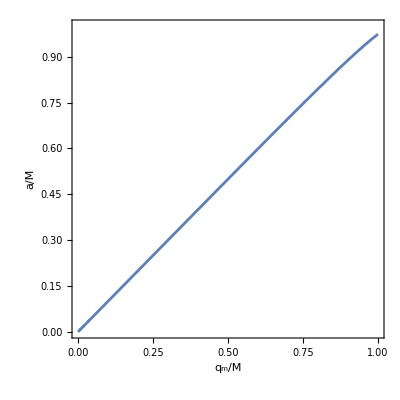

```mathematica
ContourPlot[1+√(1-a^2)-rh[q]==0,{q,0,1},{a,0,1},AspectRatio->1,LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},Frame->True,FrameLabel->{"q_m/M"," a/M"}]
```

## Effective Potential

```mathematica
Clear[Veff]
```

```mathematica
Veff[r_,q_,L_] = f[r,q](1+ L^2/r^2)
```

(1+L^2/r^2) (1-(2 (1-Tanh[q^2/(2 r)]))/r)

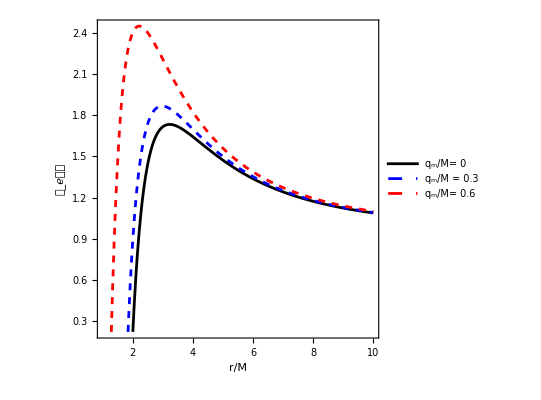

```mathematica
Plot[{Veff[r,0.3,6],Veff[r,0.6,6],Veff[r,0.99,6]},{r,1,10}(*,PlotRange->{{1,10},{0,2.45}}*),FrameLabel->{"r/M","𝒱_ℯ𝒻𝒻"},Frame->True,AspectRatio->1,PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},PlotLegends->Placed[{"q_m/M= 0","q_m/M = 0.3","q_m/M= 0.6"},{Scaled[{0.72,0.26}], {0.4, 0.5}}]]
```

## Specific energy and angular momentum

```mathematica
Clear[Ω]
```

```mathematica
Ω[r_,q_] = √((- D[gtt,r])/D[gϕϕ,r]);
Ll[r_,q_]=(Ω[r,q] gϕϕ)/(√(-gtt -Ω[r,q]^2 gϕϕ)) (*√((D[f[r,q],r] r^3)/(2 f[r,q] r - D[f[r,q],r]))*)//FullSimplify;

Ene[r_,q_] = -gtt/(√(-gtt -Ω[r,q]^2 gϕϕ));
```

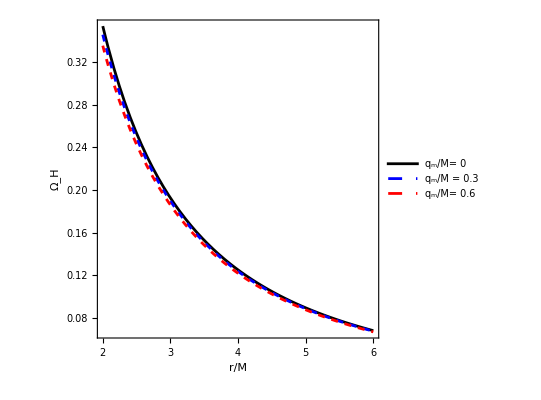

```mathematica
Plot[{Ω[r,0.],Ω[r,0.3],Ω[r,0.45]},{r,2,6},AspectRatio->1,PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},PlotLegends->Placed[{"q_m/M= 0","q_m/M = 0.3","q_m/M= 0.6"},{Scaled[{0.72,0.86}], {0.4, 0.5}}],Frame->True,FrameLabel->{"r/M","Ω_H"},

Epilog->Inset[Plot[{Ω[r,0.],Ω[r,0.3],Ω[r,0.45]},{r,3.5,3.8},PlotRange->{{3.5,3.8},{0.135,0.15}},Frame->True,PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 10}],Scaled[{0.7,0.5}]]
]
```

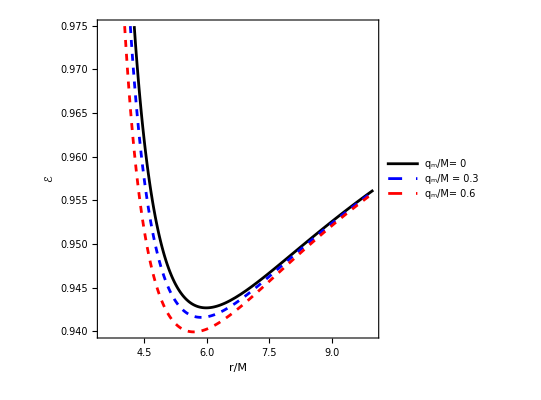

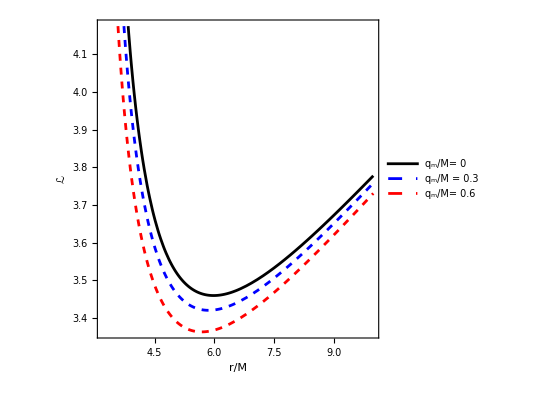

```mathematica
Plot[{Ene[r,0.1],Ene[r,0.3],Ene[r,0.45]},{r,3.5,10},AspectRatio->1,PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},PlotLegends->Placed[{"q_m/M= 0","q_m/M = 0.3","q_m/M= 0.6"},{Scaled[{0.72,0.66}], {0.4, 0.5}}],Frame->True,FrameLabel->{"r/M","ℰ"}]

Plot[{Ll[r,0.1],Ll[r,0.3],Ll[r,0.45]},{r,3.2,10},PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},PlotLegends->Placed[{"q_m/M= 0","q_m/M = 0.3","q_m/M= 0.6"},{Scaled[{0.72,0.66}], {0.4, 0.5}}],AspectRatio->1,Frame->True,FrameLabel->{"r/M","ℒ"}]
```

## ISCO radii

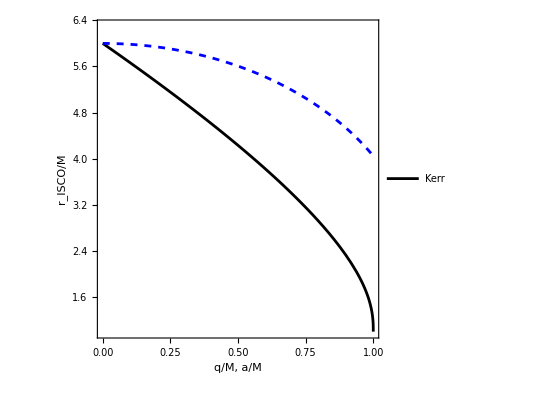

```mathematica
risc[q_]:=r/.FindRoot[D[Ll[r,q],r]==0,{r,5}](* massive particles ISCO of ζ distribution *)
z1 =1+(1-a^2)^(1/3)((1+a)^(1/3)+(1-a)^(1/3));
z2 = Sqrt[3 a^2 + z1^2];
rk[a_]=3+z2-If[a<0,-1,1]Sqrt[(3-z1)(3+z1+2 z2)]   ;    (* Kerr metric isco radii *)

Plot[{rk[x],If[x<0,None,risc[x]]},{x,0,1},Frame->True,FrameLabel->{"q/M,  a/M","r_ISCO/M"},PlotRange->{{0,1},{1,6.3}},PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},PlotLegends->Placed[{"Kerr"},{Scaled[{0.72,0.48}], {0.4, 0.5}}],AspectRatio->1]
```

FindRoot::nlnum: The function value {(2. √(-1. q^2 Sech[«1»]^2-10. (-1.+Tanh[«1»])))/(√(q^2 Sech[«1»]^2+10. (2.+Times[«2»])))+(1562.5 (0.00128 «1»-«1»))/(√(-1. q^2 («1»)^2-10. «1») √(«1»))-(62.5 √(«1») (0.04 (10. Plus[«2»]+0.04 Power[«2»] Power[«2»] Tanh[«1»]+2. Plus[«2»])-0.016 «1»))/((q^2 Sech[«1»]^2+10. (2.+Times[«2»]))^(3/2))} is not a list of numbers with dimensions {1} at {r} = {5.}.

ReplaceAll::reps: {FindRoot[∂_r Ll[r,q]==0,{r,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2. √(-1. q^2 Sech[«1»]^2-10. (-1.+Tanh[«1»])))/(√(q^2 Sech[«1»]^2+10. (2.+Times[«2»])))+(1562.5 (0.00128 «1»-«1»))/(√(-1. q^2 («1»)^2-10. «1») √(«1»))-(62.5 √(«1») (0.04 (10. Plus[«2»]+0.04 Power[«2»] Power[«2»] Tanh[«1»]+2. Plus[«2»])-0.016 «1»))/((q^2 Sech[«1»]^2+10. (2.+Times[«2»]))^(3/2))} is not a list of numbers with dimensions {1} at {r} = {5.}.

ReplaceAll::reps: {FindRoot[∂_r Ll[r,q]==0,{r,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(2. √(-1. q^2 Sech[«1»]^2-10. (-1.+Tanh[«1»])))/(√(q^2 Sech[«1»]^2+10. (2.+Times[«2»])))+(1562.5 (0.00128 «1»-«1»))/(√(-1. q^2 («1»)^2-10. «1») √(«1»))-(62.5 √(«1») (0.04 (10. Plus[«2»]+0.04 Power[«2»] Power[«2»] Tanh[«1»]+2. Plus[«2»])-0.016 «1»))/((q^2 Sech[«1»]^2+10. (2.+Times[«2»]))^(3/2))} is not a list of numbers with dimensions {1} at {r} = {5.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_r Ll[r,q]==0,{r,5}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

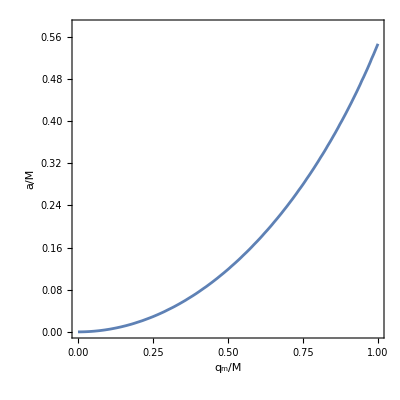

```mathematica
ContourPlot[risc[q]-rk[a]==0,{q,0,1},{a,0,0.58},FrameLabel->{"q_m/M","a/M"},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},Frame->True]
```

## Radiative efficiency

```mathematica
η[q_]:= 1- Ene[risc[q],q]
```

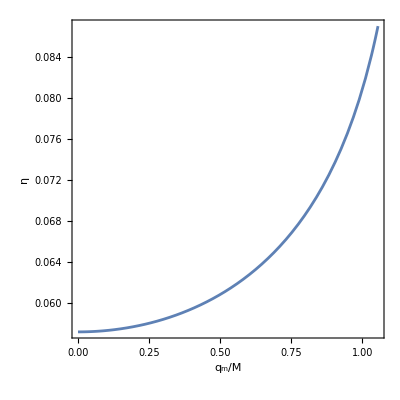

```mathematica
Plot[η[q],{q,0,1.0554},Frame->True,FrameLabel->{"q_m/M","η"},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},AspectRatio->1]
```

## Radiative flux

```mathematica
g = {{gtt,0,0,0},{0,grr,0,0},{0,0,gθθ,0},{0,0,0,gϕϕ}};
Det[g];
```

```mathematica
(*Fundamental constants*)
c=3 10^10;
G=6.67 10^-8;
h=6.626 10^-27;
k=1.38 10^-16;
σ=5.67 10^-5;


(*Parameters of the black hole and Accretion disc*)

M0=2 10^33;(*Solar mass*)
M=1;(*Normalization of radial coordinate r->r/M*)
ris=6M; (*ISCO position*)

x=10; (*Ration of black hole mass to Solar mass x=M/M0*)
m=(G M0)/c^2 x; (*Mass of black hole in unit of length*) 
Medd=2.23 10^18 x; (*Eddington mass accretion rate in x=M/M0*) 
Ratio=0.5;
Mdot=Ratio Medd;(*Mass accretion rate in x=M/M0*)

F0=(3Mdot c^2)/(8π m^2);(*Subscript[F, 0] maximum energy emission rate of thin disc*)
rmax=5 r0; (*chosen range of the radial coordinate*)
```

```mathematica
Clear[F,kr]
```

```mathematica
Clear[F]
```

```mathematica
kr[r_,q_]=D[Ω[r,q],r]/(√(-Det[g]) (Ene[r,q]- Ω[r,q] Ll[r,q])^2) ;
F[rarb_,q_]:=(-Mdot c^2)/(4 π m^2) kr[rarb,q] (NIntegrate[(Ene[r,q]- Ω[r,q] Ll[r,q]) D[Ll[r,q],r],{r,risc[q],rarb}])
```

```mathematica
f1=LogLinearPlot[{If[rarb<6.09,None,F[rarb,0]],If[rarb<6.0,None,F[rarb,0.3]],If[rarb<=5.43,None,F[rarb,0.6]]},{rarb,5.5,25},PlotLegends->Placed[{"q_m/M = 0","q_m/M = 0.3","q_m/M = 0.6"},{Scaled[{0.75,0.78}], {0.4, 0.5}}],FrameLabel->{"r/M","Φ(𝓇)"},Frame->True,LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},AspectRatio->1,PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}}]
```

-Graphics-

```mathematica
F[8.76,10^-6]//N
```

6.88539×10^21

## Temperature (𝒯)

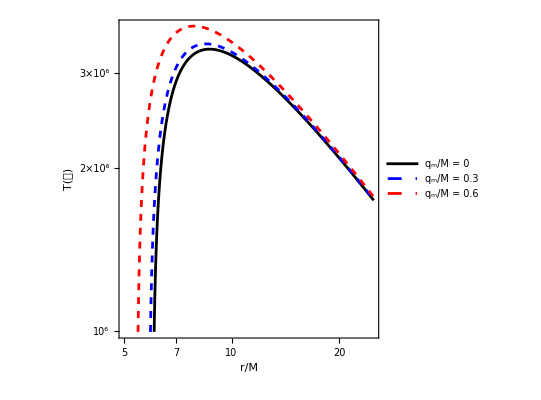

```mathematica
T[r_,q_]:=(F[r,q]/σ)^(1/4)   (* The Disk's Temperature profile *)
LogLogPlot[{If[r<=6,None,T[r,0]],If[r<=5.855,None,T[r,0.3]],If[r<=5.42,None,T[r,0.6]]},{r,5.,25},PlotLegends->Placed[{"q_m/M = 0","q_m/M = 0.3","q_m/M = 0.6"},{Scaled[{0.73,0.28}], {0.4, 0.5}}],FrameLabel->{"r/M","T(𝓇)"},Frame->True,LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},AspectRatio->1,PlotStyle->{Black,{Blue,Dashed},{Red,Dashed}}]
```

## Luminosity of the radiation ℒ(ν)

```mathematica
z[r_,q_,i_,ϕ_]=(1+Ω[r,q] r Sin[i]Sin[ϕ])/(√(-gtt-Ω[r,q]^2 gϕϕ));k=1.38*10^-16;
```

```mathematica
Clear[Lν1]
```

```mathematica
int[r_,q_,i_,ν_,ϕ_ ]:=(8π  m^2 h Cos[i])/c^2(ν^4 z[r,q,i,ϕ]^4 r)/(Exp[(h ν z[r,q,i,ϕ])/(k T[r,q])]-1);
Lν[ν_]:=NIntegrate[int[x,0,π/6,ν,ϕ ],{x,6,10^4},{ϕ,0,2π}](*aa=0, i=π/6*)
Lν2[ν_]:=NIntegrate[int[x,0.3,π/6,ν,ϕ ],{x,risc[0.3],10^4},{ϕ,0,2π}](*aa=0.3, i=π/6*)
Lν3[ν_]:=NIntegrate[int[x,0.6,π/6,ν,ϕ ],{x,risc[0.6],10^4},{ϕ,0,2π}](*aa=0.6, i=π/6*)
```

```mathematica
v0=10^13; 
t1=TimeUsed[];
Do[v[i]=v0 2;y[i]=Lν[v[i]]; v0=v[i], {i,1,14}]//Quiet
Do[v[i]=v0 1.360790000174377;y[i]=Lν[v[i]]; v0=v[i], {i,15,53}]//Quiet
data1=Table[{v[i],y[i]},{i,1,53}]
t2=TimeUsed[];
Print["total time spent is ", t2-t1, " seconds"]
```

```mathematica
data1={{20000000000000,1.93097242742273*^29},{40000000000000,1.4780150608691573*^30},{80000000000000,1.0821194845547818*^31},{160000000000000,7.254742661934017*^31},{320000000000000,4.136149838341749*^32},{640000000000000,1.8900244133953743*^33},{1280000000000000,7.554652119393904*^33},{2560000000000000,2.953660784998086*^34},{5120000000000000,1.142737633646877*^35},{10240000000000000,4.340151374319427*^35},{20480000000000000,1.5879837759573055*^36},{40960000000000000,5.342587731636462*^36},{81920000000000000,1.4683063176508677*^37},{163840000000000000,2.44346476633237*^37},{2.2295183362856992*^17,2.2229438967404027*^37},{3.033906257222993*^17,1.4644643379296558*^37},{4.12850929629552*^17,6.190886941692178*^36},{5.6180341660258976*^17,1.4467765536657292*^36},{7.644964713766036*^17,1.5438260573274804*^35},{1.040319153417879*^18,5.767766437678742*^33},{1.4156559009609231*^18,5.1406315914170715*^31},{1.9264103937154724*^18,6.375356083022584*^28},{2.621439999999999*^18,5.286590901149859*^24},{3.567229338057117*^18,1.0892818188730747*^19},{4.854250011556787*^18,1.457726531146161*^11},{6.60561487407283*^18,0.},{8.988854665641433*^18,0.},{1.2231943542025654*^19,0.},{1.6645106454686058*^19,0.},{2.265049441537476*^19,0.},{3.0822566299447546*^19,0.},{4.194303999999997*^19,0.},{5.707566940891385*^19,0.},{7.766800018490856*^19,0.},{1.0568983798516523*^20,0.},{1.4382167465026286*^20,0.},{1.9571109667241037*^20,0.},{2.663217032749768*^20,0.},{3.6240791064599606*^20,0.},{4.9316106079116054*^20,0.},{6.710886399999992*^20,0.},{9.132107105426213*^20,0.},{1.2426880029585365*^21,0.},{1.691037407762643*^21,0.},{2.3011467944042048*^21,0.},{3.131377546758565*^21,0.},{4.2611472523996273*^21,0.},{5.798526570335935*^21,0.},{7.890576972658565*^21,0.},{1.0737418239999983*^22,0.},{1.4611371368681935*^22,0.},{1.9883008047336575*^22,0.},{2.7056598524202274*^22,0.}};
```

total time spent is 661.206 seconds

```mathematica
v0=10^13; 
t1=TimeUsed[];
Do[v[i]=v0 2;y[i]=Lν2[v[i]]; v0=v[i], {i,1,14}]//Quiet
Do[v[i]=v0 1.360790000174377;y[i]=Lν2[v[i]]; v0=v[i], {i,15,53}]//Quiet
data2=Table[{v[i],y[i]},{i,1,53}]
t2=TimeUsed[];
Print["total time spent is ", t2-t1, " seconds"]
```

```mathematica
data2={{20000000000000,1.931412563803292*^29},{40000000000000,1.4783666908533337*^30},{80000000000000,1.0823992644890654*^31},{160000000000000,7.25693440566129*^31},{320000000000000,4.137779178563737*^32},{640000000000000,1.8911027219497332*^33},{1280000000000000,7.56116148946054*^33},{2560000000000000,2.9575848472968047*^34},{5120000000000000,1.1451429230409577*^35},{10240000000000000,4.3551213746693565*^35},{20480000000000000,1.597346291834455*^36},{40960000000000000,5.399431726510796*^36},{81920000000000000,1.4985451751263258*^37},{163840000000000000,2.548633202867225*^37},{2.2295183362856992*^17,2.3579666469698354*^37},{3.033906257222993*^17,1.5902115542246928*^37},{4.12850929629552*^17,6.939738895589686*^36},{5.6180341660258976*^17,1.692306131525496*^36},{7.644964713766036*^17,1.911827011612787*^35},{1.040319153417879*^18,7.71808752110377*^33},{1.4156559009609231*^18,7.650722894821432*^31},{1.9264103937154724*^18,1.097868493856353*^29},{2.621439999999999*^18,1.1112378232200322*^25},{3.567229338057117*^18,3.0048206316773028*^19},{4.854250011556787*^18,5.822838496772485*^11},{6.60561487407283*^18,0.},{8.988854665641433*^18,0.},{1.2231943542025654*^19,0.},{1.6645106454686058*^19,0.},{2.265049441537476*^19,0.},{3.0822566299447546*^19,0.},{4.194303999999997*^19,0.},{5.707566940891385*^19,0.},{7.766800018490856*^19,0.},{1.0568983798516523*^20,0.},{1.4382167465026286*^20,0.},{1.9571109667241037*^20,0.},{2.663217032749768*^20,0.},{3.6240791064599606*^20,0.},{4.9316106079116054*^20,0.},{6.710886399999992*^20,0.},{9.132107105426213*^20,0.},{1.2426880029585365*^21,0.},{1.691037407762643*^21,0.},{2.3011467944042048*^21,0.},{3.131377546758565*^21,0.},{4.2611472523996273*^21,0.},{5.798526570335935*^21,0.},{7.890576972658565*^21,0.},{1.0737418239999983*^22,0.},{1.4611371368681935*^22,0.},{1.9883008047336575*^22,0.},{2.7056598524202274*^22,0.}};
```

total time spent is 1400.98 seconds

```mathematica
v0=10^13; 
t1=TimeUsed[];
Do[v[i]=v0 2;y[i]=Lν3[v[i]]; v0=v[i], {i,1,14}]//Quiet
Do[v[i]=v0 1.360790000174377;y[i]=Lν3[v[i]]; v0=v[i], {i,15,53}]//Quiet
data3=Table[{v[i],y[i]},{i,1,53}]
t2=TimeUsed[];
Print["total time spent is ", t2-t1, " seconds"]
```

```mathematica
data3={{20000000000000,1.93283534560361*^29},{40000000000000,1.4795033512487204*^30},{80000000000000,1.0833037188747926*^31},{160000000000000,7.264021005646362*^31},{320000000000000,4.143050834912844*^32},{640000000000000,1.8945982990392762*^33},{1280000000000000,7.582331116200035*^33},{2560000000000000,2.970400277727975*^34},{5120000000000000,1.1530349880263437*^35},{10240000000000000,4.404491163747269*^35},{20480000000000000,1.6283989563781633*^36},{40960000000000000,5.589416227756994*^36},{81920000000000000,1.6011493182046247*^37},{163840000000000000,2.9197734131719774*^37},{2.2295183362856992*^17,2.8508422377927694*^37},{3.033906257222993*^17,2.0724216080310388*^37},{4.12850929629552*^17,1.0016256431869215*^37},{5.6180341660258976*^17,2.800216746582301*^36},{7.644964713766036*^17,3.7982790893216394*^35},{1.040319153417879*^18,1.9650323430909741*^34},{1.4156559009609231*^18,2.7373928839671836*^32},{1.9264103937154724*^18,6.266117071895136*^29},{2.621439999999999*^18,1.2009129589674957*^26},{3.567229338057117*^18,7.754729428283776*^20},{4.854250011556787*^18,4.918607392052917*^13},{6.60561487407283*^18,0.},{8.988854665641433*^18,0.},{1.2231943542025654*^19,0.},{1.6645106454686058*^19,0.},{2.265049441537476*^19,0.},{3.0822566299447546*^19,0.},{4.194303999999997*^19,0.},{5.707566940891385*^19,0.},{7.766800018490856*^19,0.},{1.0568983798516523*^20,0.},{1.4382167465026286*^20,0.},{1.9571109667241037*^20,0.},{2.663217032749768*^20,0.},{3.6240791064599606*^20,0.},{4.9316106079116054*^20,0.},{6.710886399999992*^20,0.},{9.132107105426213*^20,0.},{1.2426880029585365*^21,0.},{1.691037407762643*^21,0.},{2.3011467944042048*^21,0.},{3.131377546758565*^21,0.},{4.2611472523996273*^21,0.},{5.798526570335935*^21,0.},{7.890576972658565*^21,0.},{1.0737418239999983*^22,0.},{1.4611371368681935*^22,0.},{1.9883008047336575*^22,0.},{2.7056598524202274*^22,0.}};
```

ListLogLogPlot::ioproc: {{30.6268,67.433},{31.3199,69.4683},{32.013,71.4591},{32.7062,73.3618},«4»,{36.1719,80.7239},{36.8651,82.0584},«43»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListLogLogPlot::ioproc: {{30.6268,67.4332},{31.3199,69.4685},{32.013,71.4593},{32.7062,73.3621},«4»,{36.1719,80.726},{36.8651,82.0618},«43»} may contain non-machine-precision numbers, complex numbers, or invalid entries.

ListLogLogPlot::ioproc: «1» may contain non-machine-precision numbers, complex numbers, or invalid entries.

General::stop: Further output of ListLogLogPlot::ioproc will be suppressed during this calculation.

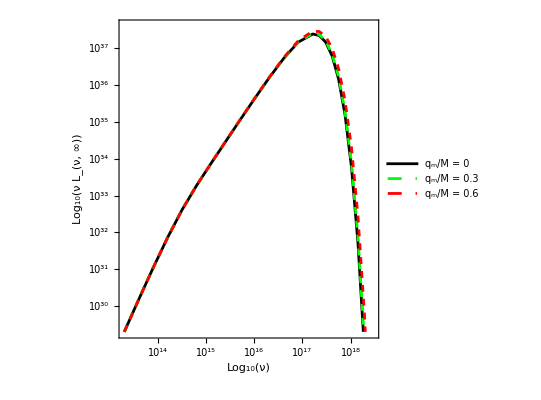

```mathematica
ListLogLogPlot[{data1,data2,data3},PlotRange->{{2*10^13,3*10^18},{2*10^29,4*10^37}},Joined->True,InterpolationOrder->5,Frame->True,FrameLabel->{"Log_10(ν)","Log_10(ν L_(ν,  ∞))"},PlotLegends->Placed[{"q_m/M = 0","q_m/M = 0.3","q_m/M = 0.6"},{0.22,0.8}],PlotStyle->{{Black},{Green,Dashed},{Red,Dashed}},LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12},AspectRatio->1(*,

Epilog->Inset[ListLogLogPlot[{data1,data2,data3},PlotRange->{{8.2*10^16,4.2*10^17},{1*10^37,3*10^37}},Joined->True,InterpolationOrder->5,Frame->True,PlotStyle->{{Black},{Green,Dashed},{Red,Dashed}},LabelStyle->Directive[Black]],Scaled[{0.7,0.3}]]*)]
```

```mathematica
ListLogLinearPlot[{data1,data2,data3},PlotRange->{{2*10^15,3*10^18},{2*10^29,4*10^37}},Joined->True,InterpolationOrder->5,Frame->True,FrameLabel->{"ν [Hz]","ν L(ν) [erg/s]"},PlotLegends->Placed[{"q/M = 0","q/M = 0.3","q/M = 0.6"},{0.15,0.81}],PlotStyle->{{Black},{Green,Dashed},{Red,Dashed}},LabelStyle->Directive[Black](*,

Epilog->Inset[ListLogLogPlot[{data1,data2,data3},PlotRange->{{6.6*10^20,1.2*10^21},{2*10^46,4.2*10^48}},Joined->True,InterpolationOrder->5,Frame->True,PlotStyle->{{Black},{Green,Dashed},{Blue,Dashed}},LabelStyle->Directive[Black]],Scaled[{0.7,0.3}]]*)]
```

-Graphics-

```mathematica
bn1=2 10^17; b11=2 10^15; n1=14; q1=(bn1/b11)^(1/(n1-1));
bn2=2 10^18; b12=2 10^17; n2=9; q2=(bn2/b12)^(1/(n2-1));
```

```mathematica
v0=b11; 
t1=TimeUsed[];
Do[v[i]=v0 q1;y[i]=Lν[v[i]]; v0=v[i], {i,1,14}]//Quiet
Do[v[i]=v0 q2;y[i]=Lν[v[i]]; v0=v[i], {i,15,23}]//Quiet
data11=Table[{v[i] 10^-18,y[i] 10^-37},{i,1,23}]
t2=TimeUsed[];
Print["total time spent is ", t2-t1, " seconds"]
```

```mathematica
data11={{1/(50 10^(11/13)),0.003645396451564191},{1/(50 10^(9/13)),0.00728361233601127},{1/(50 10^(7/13)),0.014497497936645525},{1/(50 10^(5/13)),0.02870551853438684},{1/(50 10^(3/13)),0.05641676721604952},{1/(50 10^(1/13)),0.10967806952964795},{1/(5 10^(12/13)),0.20975449787635575},{1/(5 10^(10/13)),0.3911553228350926},{1/(5 10^(8/13)),0.7012060717484425},{1/(5 10^(6/13)),1.1808230755385791},{1/(5 10^(4/13)),1.7997378690890893},{1/(5 10^(2/13)),2.3402167776562908},{1/5,2.371610304336786},{2^(2/13)/5^(11/13),1.644888009792897},{2^(29/104)/5^(75/104),0.8212437665902419},{2^(21/52)/5^(31/52),0.25389249239313694},{2^(55/104)/5^(49/104),0.04211954773595997},{2^(17/26)/5^(9/26),0.003101409314536464},{2^(81/104)/5^(23/104),0.00007765723719451672},{2^(47/52)/5^(5/52),4.555125876979489*^-7},{2 10^(3/104),3.784007911403001*^-10},{2 10^(2/13),2.2850707491613453*^-14},{2 10^(29/104),4.1444031509414475*^-20}};
```

total time spent is 568.902 seconds

```mathematica
(*data11={{2000000000000000 10^(2/13),3.6453964515641907*^34},{2000000000000000 10^(4/13),7.283612336011269*^34},{2000000000000000 10^(6/13),1.4497497936645523*^35},{2000000000000000 10^(8/13),2.870551853438684*^35},{2000000000000000 10^(10/13),5.641676721604951*^35},{2000000000000000 10^(12/13),1.0967806952964795*^36},{20000000000000000 10^(1/13),2.0975449787635573*^36},{20000000000000000 10^(3/13),3.911553228350925*^36},{20000000000000000 10^(5/13),7.012060717484425*^36},{20000000000000000 10^(7/13),1.1808230755385791*^37},{20000000000000000 10^(9/13),1.7997378690890892*^37},{20000000000000000 10^(11/13),2.3402167776562907*^37},{200000000000000000,2.371610304336786*^37},{200000000000000000 10^(2/13),1.644888009792897*^37},{200000000000000000 10^(29/104),8.212437665902419*^36},{200000000000000000 10^(21/52),2.5389249239313693*^36},{200000000000000000 10^(55/104),4.2119547735959965*^35},{200000000000000000 10^(17/26),3.1014093145364636*^34},{200000000000000000 10^(81/104),7.765723719451671*^32},{200000000000000000 10^(47/52),4.555125876979489*^30},{2000000000000000000 10^(3/104),3.784007911403001*^27},{2000000000000000000 10^(2/13),2.2850707491613453*^23},{2000000000000000000 10^(29/104),4.144403150941447*^17}};*)
```

```mathematica
v0=b11; 
t1=TimeUsed[];
Do[v[i]=v0 q1;y[i]=Lν2[v[i]]; v0=v[i], {i,1,14}]//Quiet
Do[v[i]=v0 q2;y[i]=Lν2[v[i]]; v0=v[i], {i,15,23}]//Quiet
data22=Table[{v[i],y[i]},{i,1,23}]
t2=TimeUsed[];
Print["total time spent is ", t2-t1, " seconds"]
```

```mathematica
data22={{2000000000000000 10^(2/13),3.6505873628404608*^34},{2000000000000000 10^(4/13),7.296714443008297*^34},{2000000000000000 10^(6/13),1.453071277883124*^35},{2000000000000000 10^(8/13),2.8790049142284182*^35},{2000000000000000 10^(10/13),5.66324919615447*^35},{2000000000000000 10^(12/13),1.1022893778446567*^36},{20000000000000000 10^(1/13),2.1115649078200202*^36},{20000000000000000 10^(3/13),3.946870223377745*^36},{20000000000000000 10^(5/13),7.099063821376709*^36},{20000000000000000 10^(7/13),1.2013516080418001*^37},{20000000000000000 10^(9/13),1.8445014912991981*^37},{20000000000000000 10^(11/13),2.4251670048552697*^37},{200000000000000000,2.499116034911109*^37},{200000000000000000 10^(2/13),1.776576010066631*^37},{200000000000000000 10^(29/104),9.118944600345591*^36},{200000000000000000 10^(21/52),2.923796168812113*^36},{200000000000000000 10^(55/104),5.0878338517212494*^35},{200000000000000000 10^(17/26),3.9909764594034476*^34},{200000000000000000 10^(81/104),1.0877079824876565*^33},{200000000000000000 10^(47/52),7.150795322438438*^30},{2000000000000000000 10^(3/104),6.922292387889836*^27},{2000000000000000000 10^(2/13),5.129431378603211*^23},{2000000000000000000 10^(29/104),1.222676294444031*^18}};
```

```mathematica
v0=b11; 
t1=TimeUsed[];
Do[v[i]=v0 q1;y[i]=Lν3[v[i]]; v0=v[i], {i,1,14}]//Quiet
Do[v[i]=v0 q2;y[i]=Lν3[v[i]]; v0=v[i], {i,15,23}]//Quiet
data33=Table[{v[i],y[i]},{i,1,23}]
t2=TimeUsed[];
Print["total time spent is ", t2-t1, " seconds"]
```

```mathematica
data33={{2000000000000000 10^(2/13),3.6675518500728057*^34},{2000000000000000 10^(4/13),7.3396383185079185*^34},{2000000000000000 10^(6/13),1.4639790253533009*^35},{2000000000000000 10^(8/13),2.9068367815228205*^35},{2000000000000000 10^(10/13),5.734469275445257*^35},{2000000000000000 10^(12/13),1.1205282219148188*^36},{20000000000000000 10^(1/13),2.158131481899317*^36},{20000000000000000 10^(3/13),4.064620649928085*^36},{20000000000000000 10^(5/13),7.39060975622753*^36},{20000000000000000 10^(7/13),1.270658786818462*^37},{20000000000000000 10^(9/13),1.9974528869228113*^37},{20000000000000000 10^(11/13),2.721266162366888*^37},{200000000000000000,2.95831960830168*^37},{200000000000000000 10^(2/13),2.2758232571003354*^37},{200000000000000000 10^(29/104),1.276691522575518*^37},{200000000000000000 10^(21/52),4.601480313057563*^36},{200000000000000000 10^(55/104),9.333805373457479*^35},{200000000000000000 10^(17/26),8.9659006774159*^34},{200000000000000000 10^(81/104),3.204895656223585*^33},{200000000000000000 10^(47/52),3.034834658566623*^31},{2000000000000000000 10^(3/104),4.794604567982612*^28},{2000000000000000000 10^(2/13),6.841744173252178*^24},{2000000000000000000 10^(29/104),3.912910318429989*^19}};
```

```mathematica
ListLogLinearPlot[{data11(*,data22,data33*)},PlotRange->{{3 10^15,1 10^18},{0.1 10^27,3.3 10^37}}, Joined->True, InterpolationOrder->5,  Frame->True,FrameLabel->{"ν ,  [Hz]_","ν L_(ν)_,  [erg/s]"},PlotLegends->Placed[{"q_m/M = 0","q_m/M = 0.3","q_m/M = 0.6"},{Scaled[{0.23,0.75}], {0.4, 0.5}}],PlotStyle->{{Black},{Blue,Dashed},{Red,Dashed}},BaseStyle->{15,Background->White},AspectRatio->1.1,LabelStyle->{FontFamily -> "Times",Black,Bold, Italic,FontSize-> 12}]
```

-Graphics-